```mathematica
Clear[D0,D2,Λ2,p0,p2]
```

```mathematica
Integrate[((σ-1/2)/(s-1/2))^2,{σ,s,1/2}]
```

1/6 (1-2 s)

```mathematica
Simplify[s+Integrate[(σ2-1/2)/(s-1/2),{σ2,s,σ}]]
```

(s^2+(-1+σ) σ)/(-1+2 s)

```mathematica
Simplify[s+((σ-1/2)^2-(s-1/2)^2)/(2(s-1/2))]
```

(s^2+(-1+σ) σ)/(-1+2 s)

```mathematica
Integrate[(1+dψmax^2/(24Ξ^2))Cos[dψmax σ],{σ,0,s}]
```

(1/dψmax+dψmax/(24 Ξ^2)) Sin[dψmax s]

```mathematica
Integrate[(1+(dψmax(σ-1/2)/(s-1/2))^2/(24Ξ^2))Cos[dψmax(s^2+σ(σ-1))/(2s-1)]-dψmax/(s-1/2)/(12Ξ^2)Sin[dψmax(s^2+σ(σ-1))/(2s-1)],{σ,s,1/2}]
```

1/(24 √dψmax √(-1+2 s) Ξ^2)(-dψmax^(3/2) √(-1+2 s) Sin[dψmax s]-3 √(2 π) FresnelC[(√dψmax √(-1+2 s))/(√(2 π))] (4 (-1+2 s) Ξ^2 Cos[1/4 dψmax (1+2 s)]-dψmax Sin[1/4 dψmax (1+2 s)])+3 √(2 π) FresnelS[(√dψmax √(-1+2 s))/(√(2 π))] (dψmax Cos[1/4 dψmax (1+2 s)]+4 (-1+2 s) Ξ^2 Sin[1/4 dψmax (1+2 s)]))

```mathematica
FullSimplify[1/(24 √dψmax √(-1+2 s) Ξ^2)(-dψmax^(3/2) √(-1+2 s) Sin[dψmax s]-3 √(2 π) FresnelC[(√dψmax √(-1+2 s))/(√(2 π))] (4 (-1+2 s) Ξ^2 Cos[1/4 dψmax (1+2 s)]-dψmax Sin[1/4 dψmax (1+2 s)])+3 √(2 π) FresnelS[(√dψmax √(-1+2 s))/(√(2 π))] (dψmax Cos[1/4 dψmax (1+2 s)]+4 (-1+2 s) Ξ^2 Sin[1/4 dψmax (1+2 s)])),Assumptions->s<1/2]
```

1/(24 √dψmax √(-1+2 s) Ξ^2)(-dψmax^(3/2) √(-1+2 s) Sin[dψmax s]+3 √(2 π) FresnelC[(√dψmax √(-1+2 s))/(√(2 π))] (4 (1-2 s) Ξ^2 Cos[1/4 dψmax (1+2 s)]+dψmax Sin[1/4 dψmax (1+2 s)])+3 √(2 π) FresnelS[(√dψmax √(-1+2 s))/(√(2 π))] (dψmax Cos[1/4 dψmax (1+2 s)]+4 (-1+2 s) Ξ^2 Sin[1/4 dψmax (1+2 s)]))

```mathematica
dψmaxeq=1/Λ-1/(2r) dψmax Λ+dψmax^2/(24 Λ Ξ^2)+(dψmax^3 Λ)/(16r Ξ^2)/.Ξ->1/ξ
```

1/Λ-(dψmax Λ)/(2 r)+(dψmax^2 ξ^2)/(24 Λ)+(dψmax^3 Λ ξ^2)/(16 r)

```mathematica
geomeq=Sqrt[r]/Λ((1/dψmax+dψmax/(24 Ξ^2)) Sin[dψmax s]+1/(24 √dψmax √(-1+2 s) Ξ^2)(-dψmax^(3/2) √(-1+2 s) Sin[dψmax s]-3 √(2 π) FresnelC[(√dψmax √(-1+2 s))/(√(2 π))] (4 (-1+2 s) Ξ^2 Cos[1/4 dψmax (1+2 s)]-dψmax Sin[1/4 dψmax (1+2 s)])+3 √(2 π) FresnelS[(√dψmax √(-1+2 s))/(√(2 π))] (dψmax Cos[1/4 dψmax (1+2 s)]+4 (-1+2 s) Ξ^2 Sin[1/4 dψmax (1+2 s)])))+Sqrt[1/r]Λ Sin[dψmax(2s+1)/4]-Sqrt[r](1-D)/.Ξ->1/ξ
```

-((1-D) √r)+√(1/r) Λ Sin[1/4 dψmax (1+2 s)]+1/Λ √r ((1/dψmax+(dψmax ξ^2)/24) Sin[dψmax s]+1/(24 √dψmax √(-1+2 s))ξ^2 (-dψmax^(3/2) √(-1+2 s) Sin[dψmax s]-3 √(2 π) FresnelC[(√dψmax √(-1+2 s))/(√(2 π))] ((4 (-1+2 s) Cos[1/4 dψmax (1+2 s)])/ξ^2-dψmax Sin[1/4 dψmax (1+2 s)])+3 √(2 π) FresnelS[(√dψmax √(-1+2 s))/(√(2 π))] (dψmax Cos[1/4 dψmax (1+2 s)]+(4 (-1+2 s) Sin[1/4 dψmax (1+2 s)])/ξ^2)))

```mathematica
energy=Λ+1/Λ+(4s+1)/(24Ξ^2Λ)dψmax^2/.Ξ->1/ξ
```

1/Λ+Λ+(dψmax^2 (1+4 s) ξ^2)/(24 Λ)

```mathematica
dψmaxeqexp=dψmaxeq/.{dψmax->p0+p2 ξ^2+p4 ξ^4+p6 ξ^6+O[ξ]^8,Λ->1+Λ2 ξ^2+Λ4 ξ^4+Λ6 ξ^6+O[ξ]^8,s->1/2+s2 ξ^2+s4 ξ^4+s6 ξ^6+O[ξ]^8}
```

(1-p0/(2 r))+(p0^2/24+p0^3/(16 r)-Λ2+(-p2-p0 Λ2)/(2 r)) ξ^2+(Λ2^2+1/24 (2 p0 p2-p0^2 Λ2)+(3 p0^2 p2+p0^3 Λ2)/(16 r)-Λ4+(-p4-p2 Λ2-p0 Λ4)/(2 r)) ξ^4+(-Λ2^3+1/24 (p2^2+2 p0 p4-2 p0 p2 Λ2+p0^2 (Λ2^2-Λ4))+2 Λ2 Λ4+(p0^3 ((3 p2^2)/p0^2+(3 p4)/p0)+3 p0^2 p2 Λ2+p0^3 Λ4)/(16 r)-Λ6+(-p6-p4 Λ2-p2 Λ4-p0 Λ6)/(2 r)) ξ^6+O[ξ]^8

```mathematica
geomeqexp=Simplify[geomeq/.{dψmax->p0+p2 ξ^2+p4 ξ^4+p6 ξ^6+O[ξ]^8,Λ->1+Λ2 ξ^2+Λ4 ξ^4+Λ6 ξ^6+O[ξ]^8,s->1/2+s2 ξ^2+s4 ξ^4+s6 ξ^6+O[ξ]^8},Assumptions->ξ>0]
```

((-1+D) √r+(√(1/r)+(√r)/p0) Sin[p0/2])+((4 p0 (p0 p2 √(1/r)+p2 √r+p0^2 √(1/r) s2) Cos[p0/2]+(p0^3 √r-8 p2 √r+8 p0^2 √(1/r) Λ2-8 p0 √r Λ2) Sin[p0/2]) ξ^2)/(8 p0^2)+1/(48 p0^3)(p0 (-24 p2^2 √r+4 p0^4 √r s2+24 p0 √r (p4-p2 Λ2)+24 p0^2 √(1/r) (p4+p2 (s2+Λ2))+3 p0^3 (p2 √r+8 √(1/r) (s4+s2 Λ2))) Cos[p0/2]-2 (-24 p2^2 √r+3 p0^5 √(1/r) s2^2+24 p0 √r (p4-p2 Λ2)+p0^4 (6 p2 √(1/r) s2+√r (-4 s2^2+3 Λ2))+3 p0^2 √r (p2^2-8 Λ2^2+8 Λ4)+3 p0^3 (p2^2 √(1/r)-p2 √r-8 √(1/r) Λ4)) Sin[p0/2]) ξ^4-1/(960 p0^4)(4 p0 (-120 p2^3 √r+5 p0^6 √(1/r) s2^3-120 p0 p2 √r (-2 p4+p2 Λ2)+p0^5 (15 p2 √(1/r) s2^2-4 √r (4 s2^3+5 s4-5 s2 Λ2))+5 p0^2 √r (p2^3-24 p6+24 p4 Λ2-24 p2 Λ2^2+24 p2 Λ4)+5 p0^3 (p2^3 √(1/r)-3 p2^2 √r-24 √(1/r) (p6+p4 (s2+Λ2))-24 p2 √(1/r) (s4+s2 Λ2+Λ4))-5 p0^4 (3 p4 √r-3 p2^2 √(1/r) s2+p2 √r (8 s2+4 s2^2-3 Λ2)+24 √(1/r) (s6+s4 Λ2+s2 Λ4))) Cos[p0/2]+(960 p2^3 √r+28 p0^7 √r s2^2+960 p0 p2 √r (-2 p4+p2 Λ2)+40 p0^6 s2 (p2 √r+3 √(1/r) (2 s4+s2 Λ2))-120 p0^2 √r (p2^3-8 p6+8 p4 Λ2-8 p2 Λ2^2+8 p2 Λ4)+5 p0^5 (3 p2^2 √r+48 p4 √(1/r) s2+48 p2 √(1/r) (s2^2+s4+s2 Λ2)+8 √r (-8 s2 s4+4 s2^2 Λ2-3 Λ2^2+3 Λ4))-120 p0^3 √r (-2 p2 p4+p2^2 Λ2-8 (Λ2^3-2 Λ2 Λ4+Λ6))+40 p0^4 (6 p2 p4 √(1/r)+3 p2^2 √(1/r) (2 s2+Λ2)+p2 √r (-4 s2^2+3 Λ2)-3 (p4 √r+8 √(1/r) Λ6))) Sin[p0/2]) ξ^6+O[ξ]^7

```mathematica
energyexp=energy/.{dψmax->p0+p2 ξ^2+p4 ξ^4+p6 ξ^6+O[ξ]^8,Λ->1+Λ2 ξ^2+Λ4 ξ^4+Λ6 ξ^6+O[ξ]^8,s->1/2+s2 ξ^2+s4 ξ^4+s6 ξ^6+O[ξ]^8}
```

2+(p0^2 ξ^2)/8+(1/24 (6 p0 p2+p0^2 (4 s2-3 Λ2))+Λ2^2) ξ^4+(-Λ2^3+1/24 (3 (p2^2+2 p0 p4)+2 p0 p2 (4 s2-3 Λ2)+p0^2 (4 s4-4 s2 Λ2+3 (Λ2^2-Λ4)))+2 Λ2 Λ4) ξ^6+O[ξ]^8

```mathematica
Solve[1-p0/(2 r)==0,p0]
```

{{p0→2 r}}

```mathematica
p0=2r;
```

```mathematica
Simplify[(-1+D) √r+(√(1/r)+(√r)/p0) Sin[p0/2],Assumptions->r>0]
```

(2 (-1+D) r+3 Sin[r])/(2 √r)

```mathematica
Simplify[Solve[2 (-1+D) r+3 Sin[r]==0,D]]
```

{{D→1-(3 Sin[r])/(2 r)}}

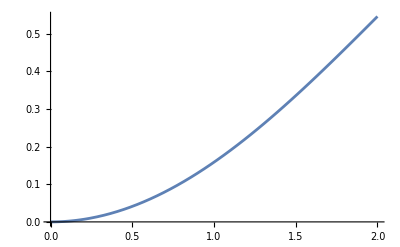

```mathematica
Plot[1-Sin[r]/r,{r,0,2}]
```

```mathematica
Simplify[energyexp+O[ξ]^6]
```

2+(r^2 ξ^2)/2+((p2 r)/2+1/6 r^2 (4 s2-3 Λ2)+Λ2^2) ξ^4+O[ξ]^6